```mathematica
refVol=Abs[Partition[BinaryReadList[NotebookDirectory[]<>"../test_data/8mm_iso_x_rot_0_5_to_2_5_deg_z_trans_rep_0_slice_"<>ToString[#]<>".dat","Complex64"],32]&/@Range[0,31,1]];
```

```mathematica
scale=1/Max[refVol]
```

15.3553

```mathematica
refVolScaled=scale * refVol;
```

```mathematica
BinaryWrite[NotebookDirectory[]<>"refVolInput.dat",refVolScaled,"Real64"];
```

```mathematica
newVolScaled=scale * Abs[Partition[BinaryReadList[NotebookDirectory[]<>"../test_data/8mm_iso_x_rot_0_5_to_2_5_deg_z_trans_rep_5_slice_"<>ToString[#]<>".dat","Complex64"],32]&/@Range[0,31,1]];
```

```mathematica
BinaryWrite[NotebookDirectory[]<>"newVolInput.dat",newVolScaled,"Real64"];
```

Compute the cooridinates of each point in the Fourier domain; note that Fourier coordinates are funny in that the origin is centered in the first voxel

```mathematica
fourierPoints=Function[{zDim,yDim,xDim},RotateLeft[Table[{i,j,k},{i,-zDim,zDim-1},{j,-yDim,yDim-1},{k,-xDim,xDim-1}],{zDim,yDim,xDim}]]@@(Dimensions[refVolScaled]/2);
```

```mathematica
Dimensions[fourierPoints]
```

{32,32,32,3}

Define the radial window function that will be applied in the Fourier domain

```mathematica
windowFunction[x_]:=If[x/16<3/4,1,HannWindow[(x/16-3/4)2]]
```

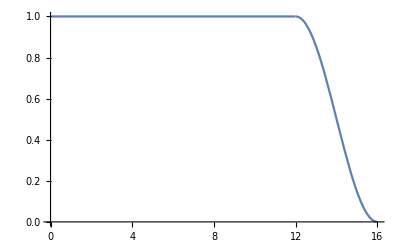

```mathematica
Plot[windowFunction[x],{x,0,16},PlotRange->All]
```

Compute the weight at each point in the Fourier domain

```mathematica
fourierWindowWeights=Map[windowFunction[Norm[#]]&,N[fourierPoints],{3}];
```

Define a function for applying the weights in the Fourier domain

```mathematica
filteredImage[img_]:=Chop[InverseFourier[Fourier[img,FourierParameters->{1, -1}] * fourierWindowWeights,FourierParameters->{1, -1}]];
```

Apply the Fourier-domain weights to each image volume

```mathematica
filteredRefVolScaled=filteredImage[refVolScaled];
```

```mathematica
filteredNewVolScaled=filteredImage[newVolScaled];
```

```mathematica
filteredRefVolScaled[[1,1,1]]
```

0.018933

```mathematica
filteredNewVolScaled[[1,1,1]]
```

0.0117165

```mathematica
points=Function[{zDim,yDim,xDim},Table[{i-(zDim/2-0.5),j-(yDim/2-0.5),k-(xDim/2-0.5)},{i,0,zDim-1},{j,0,yDim-1},{k,0,xDim-1}]]@@{32,32,32};
```

```mathematica
pointWeights[points_]:=(windowFunction[Norm[#]]&/@Flatten[points,2]);
```

```mathematica
z1=N[-2+Sqrt[3]]
```

-0.267949

```mathematica
c0=6;
```

```mathematica
computeG[x_,dataLength_]:=MapThread[Times,{FoldList[z1#1+#2&,x*c0],PadLeft[{1/(1-z1^dataLength)},dataLength,1]}]
```

```mathematica
computeYPlus[x_,dataLength_]:=Function[list,Append[MapIndexed[#1+z1^(#2[[1]])Last[list]&,list][[;;-2]],Last[list]]]@computeG[x,dataLength]
```

```mathematica
computeH[x_,dataLength_]:=Reverse[MapThread[Times,{FoldList[z1#1+#2&,Reverse[-z1 computeYPlus[x,dataLength]]]PadLeft[{1/(1-z1^dataLength)},dataLength,1]}]]
```

```mathematica
computeY[x_,dataLength_]:=Reverse[Function[list,Append[MapIndexed[#1+z1^(#2[[1]])Last[list]&,list][[;;-2]],Last[list]]]@Reverse[computeH[x,dataLength]]]
```

```mathematica
coeffImageBSpline[img_]:=Block[{
y},
(* Do x-direction calculation *)
y = Map[computeY[#,Dimensions[img][[3]]]&,img,{2}];
(* Do y-direction calculation *)
y = Map[computeY[#,Dimensions[y][[2]]]&,y];
(* Do z-direction calculation *)
y = computeY[y,Dimensions[y][[1]]];
Return[y];
];
```

This is the coefficient matrix that links the 64 coefficient values in the neighbourhood around a point, with the 64 powers of that point’s coordinates inside the cell..

```mathematica
bSplineCoeffMat={{1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0,1/54,2/27,1/54,0,2/27,8/27,2/27,0,1/54,2/27,1/54,0,0,0,0,0,1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0,-1/18,0,1/18,0,-2/9,0,2/9,0,-1/18,0,1/18,0,0,0,0,0,-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0,1/18,-1/9,1/18,0,2/9,-4/9,2/9,0,1/18,-1/9,1/18,0,0,0,0,0,1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0,-1/54,1/18,-1/18,1/54,-2/27,2/9,-2/9,2/27,-1/54,1/18,-1/18,1/54,0,0,0,0,-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0,-1/18,-2/9,-1/18,0,0,0,0,0,1/18,2/9,1/18,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0,1/6,0,-1/6,0,0,0,0,0,-1/6,0,1/6,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0,-1/6,1/3,-1/6,0,0,0,0,0,1/6,-1/3,1/6,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0,1/18,-1/6,1/6,-1/18,0,0,0,0,-1/18,1/6,-1/6,1/18,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0,1/18,2/9,1/18,0,-1/9,-4/9,-1/9,0,1/18,2/9,1/18,0,0,0,0,0,1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0,-1/6,0,1/6,0,1/3,0,-1/3,0,-1/6,0,1/6,0,0,0,0,0,-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0,1/6,-1/3,1/6,0,-1/3,2/3,-1/3,0,1/6,-1/3,1/6,0,0,0,0,0,1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0,-1/18,1/6,-1/6,1/18,1/9,-1/3,1/3,-1/9,-1/18,1/6,-1/6,1/18,0,0,0,0,-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0,-1/54,-2/27,-1/54,0,1/18,2/9,1/18,0,-1/18,-2/9,-1/18,0,1/54,2/27,1/54,0,-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0,1/18,0,-1/18,0,-1/6,0,1/6,0,1/6,0,-1/6,0,-1/18,0,1/18,0,1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0,-1/18,1/9,-1/18,0,1/6,-1/3,1/6,0,-1/6,1/3,-1/6,0,1/18,-1/9,1/18,0,-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216,1/54,-1/18,1/18,-1/54,-1/18,1/6,-1/6,1/18,1/18,-1/6,1/6,-1/18,-1/54,1/18,-1/18,1/54,1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,-1/18,-2/9,-1/18,0,-1/72,-1/18,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,1/6,0,-1/6,0,1/24,0,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,-1/6,1/3,-1/6,0,-1/24,1/12,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,1/18,-1/6,1/6,-1/18,1/72,-1/24,1/24,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,-1/6,-1/24,0,1/12,1/3,1/12,0,-1/24,-1/6,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,0,-1/8,0,-1/4,0,1/4,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,1/4,-1/8,0,1/4,-1/2,1/4,0,-1/8,1/4,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/8,1/8,-1/24,-1/12,1/4,-1/4,1/12,1/24,-1/8,1/8,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,-1/24,-1/6,-1/24,0,1/24,1/6,1/24,0,-1/72,-1/18,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,1/8,0,-1/8,0,-1/8,0,1/8,0,1/24,0,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,-1/8,1/4,-1/8,0,1/8,-1/4,1/8,0,-1/24,1/12,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,1/24,-1/8,1/8,-1/24,-1/24,1/8,-1/8,1/24,1/72,-1/24,1/24,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,-1/36,-1/9,-1/36,0,-1/9,-4/9,-1/9,0,-1/36,-1/9,-1/36,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,1/12,0,-1/12,0,1/3,0,-1/3,0,1/12,0,-1/12,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,-1/12,1/6,-1/12,0,-1/3,2/3,-1/3,0,-1/12,1/6,-1/12,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,1/36,-1/12,1/12,-1/36,1/9,-1/3,1/3,-1/9,1/36,-1/12,1/12,-1/36,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,1/12,1/3,1/12,0,0,0,0,0,-1/12,-1/3,-1/12,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,1/4,-1/2,1/4,0,0,0,0,0,-1/4,1/2,-1/4,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,-1/12,1/4,-1/4,1/12,0,0,0,0,1/12,-1/4,1/4,-1/12,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,-1/12,-1/3,-1/12,0,1/6,2/3,1/6,0,-1/12,-1/3,-1/12,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,1/4,0,-1/4,0,-1/2,0,1/2,0,1/4,0,-1/4,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,-1/4,1/2,-1/4,0,1/2,-1,1/2,0,-1/4,1/2,-1/4,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,1/12,-1/4,1/4,-1/12,-1/6,1/2,-1/2,1/6,1/12,-1/4,1/4,-1/12,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,1/36,1/9,1/36,0,-1/12,-1/3,-1/12,0,1/12,1/3,1/12,0,-1/36,-1/9,-1/36,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,-1/12,0,1/12,0,1/4,0,-1/4,0,-1/4,0,1/4,0,1/12,0,-1/12,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,1/12,-1/6,1/12,0,-1/4,1/2,-1/4,0,1/4,-1/2,1/4,0,-1/12,1/6,-1/12,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,-1/36,1/12,-1/12,1/36,1/12,-1/4,1/4,-1/12,-1/12,1/4,-1/4,1/12,1/36,-1/12,1/12,-1/36,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,-1/54,-1/216,0,-1/54,-2/27,-1/54,0,-1/216,-1/54,-1/216,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,-1/72,-1/18,-1/72,0,-1/18,-2/9,-1/18,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0},{1/72,0,-1/72,0,1/18,0,-1/18,0,1/72,0,-1/72,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,1/24,0,-1/24,0,1/6,0,-1/6,0,1/24,0,-1/24,0,0,0,0,0,-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0},{-1/72,1/36,-1/72,0,-1/18,1/9,-1/18,0,-1/72,1/36,-1/72,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,-1/24,1/12,-1/24,0,-1/6,1/3,-1/6,0,-1/24,1/12,-1/24,0,0,0,0,0,1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0},{1/216,-1/72,1/72,-1/216,1/54,-1/18,1/18,-1/54,1/216,-1/72,1/72,-1/216,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,1/72,-1/24,1/24,-1/72,1/18,-1/6,1/6,-1/18,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0},{1/72,1/18,1/72,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0},{-1/24,0,1/24,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0},{1/24,-1/12,1/24,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0},{-1/72,-1/18,-1/72,0,1/36,1/9,1/36,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,1/12,1/3,1/12,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0},{1/24,0,-1/24,0,-1/12,0,1/12,0,1/24,0,-1/24,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,-1/4,0,1/4,0,1/8,0,-1/8,0,0,0,0,0,-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0},{-1/24,1/12,-1/24,0,1/12,-1/6,1/12,0,-1/24,1/12,-1/24,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,1/4,-1/2,1/4,0,-1/8,1/4,-1/8,0,0,0,0,0,1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,-1/36,1/12,-1/12,1/36,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,-1/12,1/4,-1/4,1/12,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0},{1/216,1/54,1/216,0,-1/72,-1/18,-1/72,0,1/72,1/18,1/72,0,-1/216,-1/54,-1/216,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,1/72,1/18,1/72,0,-1/24,-1/6,-1/24,0,1/24,1/6,1/24,0,-1/72,-1/18,-1/72,0,-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0},{-1/72,0,1/72,0,1/24,0,-1/24,0,-1/24,0,1/24,0,1/72,0,-1/72,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,-1/24,0,1/24,0,1/8,0,-1/8,0,-1/8,0,1/8,0,1/24,0,-1/24,0,1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0},{1/72,-1/36,1/72,0,-1/24,1/12,-1/24,0,1/24,-1/12,1/24,0,-1/72,1/36,-1/72,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,1/24,-1/12,1/24,0,-1/8,1/4,-1/8,0,1/8,-1/4,1/8,0,-1/24,1/12,-1/24,0,-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0},{-1/216,1/72,-1/72,1/216,1/72,-1/24,1/24,-1/72,-1/72,1/24,-1/24,1/72,1/216,-1/72,1/72,-1/216,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,-1/72,1/24,-1/24,1/72,1/24,-1/8,1/8,-1/24,-1/24,1/8,-1/8,1/24,1/72,-1/24,1/24,-1/72,1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216}};
```

Define a function that takes and image and all of its derivatives, and computes the interpolation coefficients

```mathematica
coeffs[img_]:=Transpose[bSplineCoeffMat. Function[coeffImg,RotateLeft[coeffImg,#]&/@Flatten[Table[{k,j,i},{k,-1,2},{j,-1,2},{i,-1,2}],2]]@(coeffImageBSpline[img]),{4,1,2,3}];
```

Define a function that takes a set of interpolation coefficients, a rotation matrix, a translation vector (and the dimensions of the image volume), and interpolates the image at a set of points

```mathematica
transformPoints[rotMatrix_,trans_,points_,dims_,halfDims_]:=
Block[{invRot=Inverse[rotMatrix]},
Return[Map[invRot . (#-trans)&,points,{3}]];
]
```

```mathematica
wrapPoints[points_,dims_,halfDims_]:=Map[(Mod[# + halfDims +dims,dims]-halfDims)&,points,{3}]
```

```mathematica
wrapPoints[{{{{0,0,0},{15.5,15.5,15.5},{16.5,16.5,-16.5}}}},{32,32,32},{16,16,16}]
```

{{{{0,0,0},{15.5,15.5,15.5},{-15.5,-15.5,15.5}}}}

```mathematica
interpImg[coeffs_,interpGridPoints_,dims_,halfDims_]:=
Block[{
curInterpGridPoint=(Mod[# + halfDims - {0.5,0.5,0.5}+dims,dims]+{1,1,1})&/@Flatten[interpGridPoints,2],
coeffIndices,interVoxelPoints,interVoxelPointPowers},
coeffIndices=Floor[curInterpGridPoint];
interVoxelPoints=curInterpGridPoint-coeffIndices;
interVoxelPointPowers[interVoxelPoint_]:=Flatten[Outer@@Prepend[(Transpose[{{1,1,1},interVoxelPoint,interVoxelPoint^2,interVoxelPoint^3}]),Times]];
Return[
MapThread[
Function[{coeffIndex,interVoxelPoint},(coeffs[[#1,#2,#3]] &@@coeffIndex). interVoxelPointPowers[interVoxelPoint]],
{coeffIndices,interVoxelPoints}]];
]
```

```mathematica
interpImg[coeffs_,rotMatrix_,trans_,points_,dims_,halfDims_]:=
interpImg[coeffs,transformPoints[rotMatrix,trans,points,dims,halfDims],dims,halfDims];
```

```mathematica
Dimensions[coeffs[refVolScaled]]
```

{32,32,32,64}

Compute the cooridinates of each voxel in the image domain; note that image coordinates put the origin at the center of the image, so each voxel has a non-integer coordinate.

```mathematica
points=Function[{zDim,yDim,xDim},Table[{i-(zDim/2-0.5),j-(yDim/2-0.5),k-(xDim/2-0.5)},{i,0,zDim-1},{j,0,yDim-1},{k,0,xDim-1}]]@@{32,32,32};
```

```mathematica
Dimensions[points]
```

{32,32,32,3}

```mathematica
Dimensions[transformPoints[IdentityMatrix[3],{0,0,0},points,{32,32,32},{16,16,16}]]
```

{32,32,32,3}

```mathematica
Dimensions[interpImg[coeffs[refVolScaled],IdentityMatrix[3],{0,0,0},points,{32,32,32},{16,16,16}]]
```

{32768}

```mathematica
derivs[img_]:=Block[{
y,
derivX,
derivY,
derivZ},
(* Compute x-direction derivs *)
derivX=(RotateRight[img,{0,0,-1}]-RotateRight[img,{0,0,1}])/2;
(* Compute x-direction derivs *)
derivY=(RotateRight[img,{0,-1,0}]-RotateRight[img,{0,1,0}])/2;
derivZ=(RotateRight[img,{-1,0,0}]-RotateRight[img,{1,0,0}])/2;
Return[{derivX, derivY, derivZ}];
];
```

6D Registration

We want to find the linear approximation to the derivatives with respect to how an object rotating around a vector x by norm[x] radians, and then translating, will change the image. The M matrix represents this approximation, and is a function of the coordinate at which its being evaluated, so define a method to compute it given the coordinate. Note that because we’re describing the effect of moving the object, the signs are flipped vs in Martin’s paper. Also note that because my derivatives are stored in the order (dx, dy, dz), but my coordinates in the p-vector are (z,y,x,rz,ry,rx) I need to reverse the order of the rows vs in Martin’s paper.

```mathematica
M[x_]:= {{0,0,-1,-x[[2]],x[[1]],0},{0,-1,0,x[[3]],0,-x[[1]]},{-1,0,0,0,-x[[3]],x[[2]]}} ;
```

```mathematica
M[{z,y,x}]//MatrixForm
```

(0 | 0 | -1 | -y | z | 0
0 | -1 | 0 | x | 0 | -z
-1 | 0 | 0 | 0 | -x | y)

Compute the M matrix for every point in the image, giving an M tensor

```mathematica
MTensor[points_]:=Transpose[Map[M,points,{3}],{1,2,3,5,4}];
```

```mathematica
Dimensions[MTensor[points]]
```

{32,32,32,6,3}

Visualize the derivatives of the first image volume with respect to the six parameters

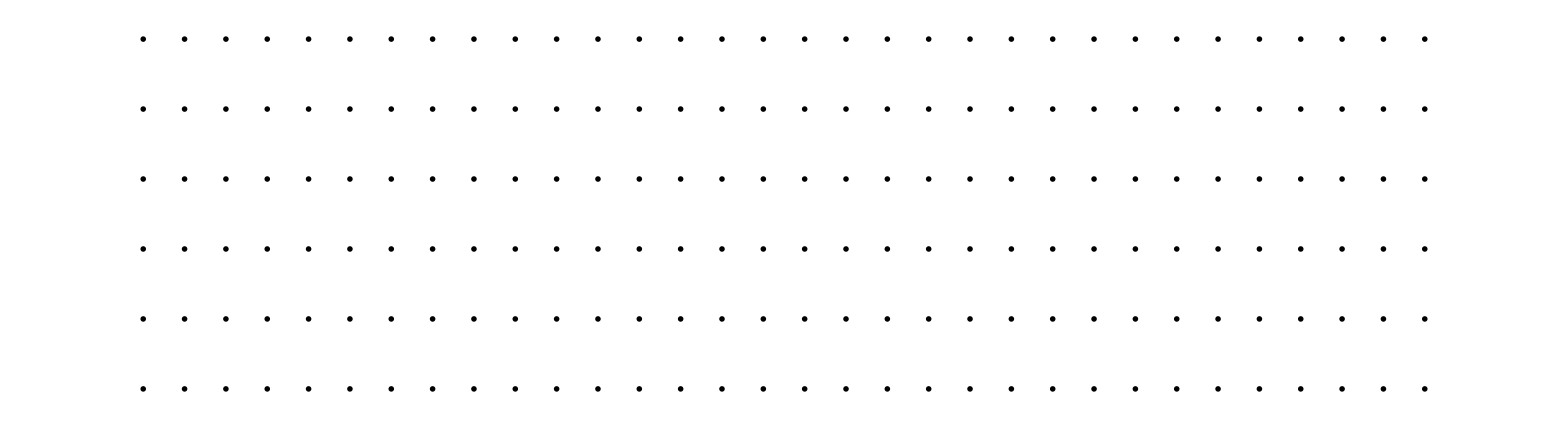

```mathematica
GraphicsGrid[Map[ArrayPlot[#,PixelConstrained->2]&,#/(2Max[#])+0.5,{2}]&@(Transpose[Partition[Partition[Flatten[MapThread[#1 . #2&,{MTensor[points],Transpose[derivs[filteredRefVolScaled],{4,1,2,3}]},3],2],32],32],{2,3,4,1}])]
```

```mathematica
Dimensions[(Transpose[Partition[Partition[Flatten[MapThread[#1 . #2&,{MTensor[points],Transpose[derivs[filteredRefVolScaled],{4,1,2,3}]},3],2],32],32],{2,3,4,1}])]
```

{6,32,32,32}

Given the gradient with respect to p, and the residual r, compute a Gauss Newton step

```mathematica
GaussNewtonStep[gradPTransGradP_,gradP_,r_]:=Block[
{deltaP,
JTransR=-Transpose[gradP] . r},
(*Print["JTransR" <> ToString[JTransR]];*)
deltaP=LinearSolve[gradPTransGradP,JTransR];
Return[deltaP]]
```

Define a utility function that takes a value of p, and prints the length of the translations in mm, the translation vector in mm, the angle of rotation in degrees, and the axis of rotation.

```mathematica
pToTransAndRot[p_]:={{Norm[p[[1;;3]]*8],p[[1;;3]]*8},{If[Norm[p[[4;;6]]]==0,0,Norm[p[[4;;6]]]/Degree],Normalize[p[[4;;6]]]}}
```

For clarity and debugging-value, let’s break these steps out and save the intermediate results in files, without all the trimming, etc.:

```mathematica
testExperiment[outputname_,accumulator_]:=Block[{
targetImg=filteredRefVolScaled,
movingImg=filteredNewVolScaled,
dims=Dimensions[filteredRefVolScaled],
halfDims=dims/2,
curPoints=points,
gradPoints=points,
targetImgCoeffs,
residualGradP,
gradPTransGradP,
r,
prevNormR=$MaxMachineNumber,
deltaP,
p={0,0,0,0,0,0},
pList,
rList={},
weightList={}},
(* compute and save the interpolation coefficients for the target image *)
targetImgCoeffs=coeffs[targetImg];
(* now start the optimization *)
pList={p};
For[i=0,i<20,i++,
(* Compute and save the residual vector by: 1) interpolating the target image at all the points based on the current p, 2) subtracting this from the moving image, 3) multiplying this difference by the weights *)
curPoints=transformPoints[
If[Norm[p[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[p[[4;;6]]],p[[4;;6]]]],
p[[1;;3]],
points,
dims,halfDims];
weightList=Append[weightList,pointWeights[wrapPoints[curPoints,dims,halfDims]]];
r=pointWeights[curPoints] *(interpImg[targetImgCoeffs,curPoints,dims,halfDims]-Flatten[movingImg]);
rList=Append[rList,r];
(* take a Gauss Newton step, save the deltaP, and update p *)
Print[Norm[r]];
If[Norm[r]>prevNormR, 
pList=pList[[;;-2]];Break[],
prevNormR = Norm[r]];
residualGradP=Transpose[(pointWeights[curPoints] * #)&/@Transpose[Flatten[MapThread[#1 . #2&,{MTensor[gradPoints],Transpose[derivs[movingImg],{4,1,2,3}]},3],2]]];
gradPTransGradP=Transpose[residualGradP]. residualGradP;
deltaP = GaussNewtonStep[gradPTransGradP,residualGradP,r];
p=accumulator[p,deltaP];
(* append this new p to our list of previous states *)
pList=Append[pList,p];
Print[p];
Print[pToTransAndRot[p]]
];
BinaryWrite[NotebookDirectory[]<>outputname,Last[pList],"Real64"];
Close[NotebookDirectory[]<>outputname];
Return[{rList,weightList}];
]
```

```mathematica
{rList,weightList}=testExperiment["parameterOutput.dat",(#1+#2)&];
```

2.82244

{-0.00576479,-0.0480781,0.0199296,-0.0475131,0.000829932,0.000222089}

{{0.418907,{-0.0461183,-0.384624,0.159437}},{2.72274,{-0.999837,0.0174646,0.00467351}}}

1.63239

{-0.00427385,-0.0349383,0.00810615,-0.0374317,0.000342459,0.000445182}

{{0.28896,{-0.0341908,-0.279506,0.0648492}},{2.14492,{-0.999887,0.00914789,0.0118919}}}

1.52792

{-0.0047651,-0.0383036,0.010458,-0.040323,0.000494858,0.000389775}

{{0.319924,{-0.0381208,-0.306429,0.0836641}},{2.31062,{-0.999878,0.0122708,0.00966513}}}

1.52593

{-0.00461183,-0.0373685,0.0098827,-0.0394972,0.000444235,0.000405962}

{{0.311419,{-0.0368946,-0.298948,0.0790616}},{2.26329,{-0.999884,0.0112459,0.010277}}}

1.52397

{-0.0046579,-0.0376311,0.0100255,-0.0397329,0.000460099,0.000401269}

{{0.31377,{-0.0372632,-0.301049,0.0802043}},{2.2768,{-0.999882,0.0115784,0.010098}}}

1.52432

This axisAngle method is taken from http://mathematica.stackexchange.com/questions/29924/axis-angle-from-rotation-matrix

```mathematica
axisAngle[m_]:=Module[{axis,ovec,nvec},{axis,ovec}=Orthogonalize[{{1,-1,1} #,Permute[#,Cycles[{{1,3,2}}]]}]&@Extract[m-Transpose[m],{{3,2},{3,1},{2,1}}];
(*nvec is orthogonal to axis and ovec:*)nvec=Cross[axis,ovec];
{axis,Arg[Complex@@(((m.ovec).#&)/@{ovec,nvec})]}]
```

```mathematica
axisAngle[IdentityMatrix[3]]
```

{{0,0,0},0}

```mathematica
AccumulateParam[oldParam_,deltaParam_]:= Block[{
oldRotationMatrix=If[Norm[oldParam[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[oldParam[[4;;6]]],oldParam[[4;;6]]]],
deltaRotationMatrix=If[Norm[deltaParam[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[deltaParam[[4;;6]]],deltaParam[[4;;6]]]],
newRotationMatrix,
newRotationAxis,
newRotationAngle},
newRotationMatrix = oldRotationMatrix . deltaRotationMatrix;
{newRotationAxis, newRotationAngle}=axisAngle[newRotationMatrix];
Return[Join[oldRotationMatrix . deltaParam[[1;;3]]+oldParam[[1;;3]], newRotationAxis * newRotationAngle]];
]
```

```mathematica
testExperiment["accumulateParameterOutput.dat",AccumulateParam];
```

2.82244

{-0.00576479,-0.0480781,0.0199296,-0.0475131,0.000829932,0.000222089}

{{0.418907,{-0.0461183,-0.384624,0.159437}},{2.72274,{-0.999837,0.0174646,0.00467351}}}

1.63239

{-0.00428677,-0.0355144,0.00749418,-0.0374315,0.000348949,0.000452517}

{{0.29239,{-0.0342942,-0.284115,0.0599534}},{2.14492,{-0.999883,0.00932125,0.0120878}}}

1.528

{-0.00476494,-0.0380938,0.0106727,-0.0403181,0.000490986,0.000386953}

{{0.318773,{-0.0381195,-0.304751,0.0853817}},{2.31033,{-0.99988,0.0121764,0.00959635}}}

1.5259

{-0.00461142,-0.037437,0.00981482,-0.0395003,0.000445844,0.000406948}

{{0.311808,{-0.0368913,-0.299496,0.0785186}},{2.26346,{-0.999883,0.0112858,0.0103012}}}

1.52398

{-0.00465803,-0.0376106,0.0100454,-0.0397315,0.00045951,0.000400948}

{{0.313654,{-0.0372643,-0.300885,0.0803628}},{2.27671,{-0.999882,0.011564,0.0100903}}}

1.52432

```mathematica
ArrayPlot[#,PixelConstrained->2,Frame->False]&/@(Partition[Partition[pointWeights[points],32],32]*filteredRefVolScaled)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}